```mathematica
<<ComputationalGeometry`
```

```mathematica
atlas=-Graphics-;
```

```mathematica
width = 1247;
height = 502;
points={{38.4707,304.151},{38.4707,243.697},{65.9498,203.394},{80.6053,159.428},{25.6471,194.234},{9.15969,232.705},{5.49581,265.68},{84.2691,322.47},{148.387,331.63},{185.026,294.991},{214.337,251.025},{194.185,342.621},{283.95,381.092},{415.85,414.067},{577.06,448.874},{727.279,492.84},{780.405,480.017},{789.565,461.697},{751.094,425.059},{707.128,388.42},{663.161,351.781},{632.019,393.916},{584.388,353.613},{507.447,331.63},{531.262,309.647},{633.85,331.63},{481.8,240.033},{483.632,316.974},{159.379,130.117},{218.001,152.1},{360.892,31.192},{227.16,163.092},{368.219,42.1836},{500.119,56.8391},{518.438,86.1501},{531.262,64.1669},{597.212,64.1669},{681.481,133.781},{741.935,135.612},{738.271,104.47},{840.859,27.5281},{904.977,38.5198},{1047.87,22.0323},{1108.32,49.5114},{1152.29,161.26},{1229.23,100.806},{1209.08,5.54488},{981.919,205.226},{937.952,236.369},{1093.67,232.705},{1113.82,276.672},{1077.18,331.63},{998.406,426.891},{897.649,491.008},{855.515,478.185},{853.683,458.033},{862.843,293.159},{818.876,456.202},{754.758,298.655},{654.002,232.705},{670.489,177.747},{747.431,186.907},{926.96,130.117},{1130.31,93.4779},{798.725,232.705},{505.615,185.075},{327.917,172.251},{327.917,265.68},{714.456,441.546},{677.817,395.748},{309.597,318.806},{566.069,410.403}};
normPoints = Map[({#[[1]] / width, #[[2]]/height})&,points];
```

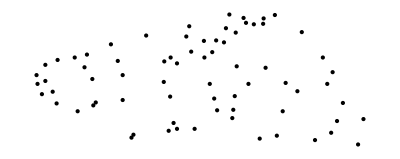

```mathematica
Graphics[Point[points]]
```

```mathematica
freq =5;
extraPoints = Join[
Table[{0,i},{i,0,1, 1/freq}],
Table[{1,i},{i,0,1, 1/freq}],
Table[{i,0},{i,0,1, 1/freq}],
Table[{i,1},{i,0,1, 1/freq}]
];
allPoints = Join[extraPoints, normPoints];
```

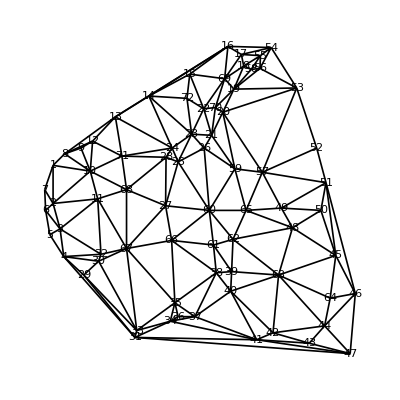

```mathematica
PlanarGraphPlot[normPoints]
```

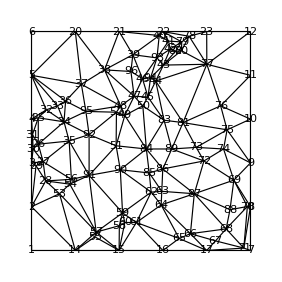

```mathematica
(* *)
PlanarGraphPlot[allPoints]
```

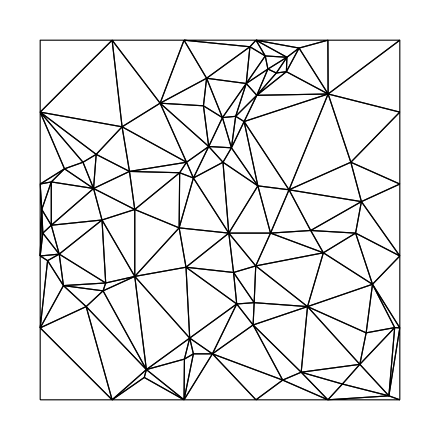

```mathematica
(* Thanks to: http://mathematica.stackexchange.com/questions/277/how-to-get-actual-triangles-from-delaunaytriangulation *)
triangles[points_]:=Module[{pl},pl=TriangularSurfacePlot[ArrayPad[points,{{0,0},{0,1}}]];
Cases[pl,Polygon[a_]:>Flatten[(Position[points,#[[{1,2}]]]&/@a)],Infinity]];

Graphics[GraphicsComplex[allPoints,{EdgeForm[Black],FaceForm[],Polygon[triangles[allPoints]]}]]
```

```mathematica
triangles[allPoints]
```

{{1,13,2,14},{2,3,29},{2,14,53},{2,28,29},{2,28,53},{3,4,31},{3,27,29},{3,27,30},{3,30,31},{4,5,32},{4,25,31},{4,25,32},{5,6,19,20},{5,20,37},{5,32,33},{5,33,36},{5,36,37},{7,18,8,71},{7,18,17,71},{8,9,69},{8,69,70},{8,70,71},{9,10,75},{9,69,74},{9,74,75},{10,11,76},{10,75,76},{11,12,24,77},{11,76,77},{12,24,23,77},{14,15,55},{14,53,57},{14,55,57},{15,16,61},{15,55,57},{15,57,58},{15,58,60},{15,60,61},{16,17,65},{16,61,65},{17,65,66},{17,66,67},{17,67,71},{20,21,38},{20,37,38},{21,22,40},{21,38,39},{21,39,40},{22,23,78},{22,40,41},{22,41,79},{22,78,79},{23,77,78},{25,26,31},{25,26,34},{25,32,34},{26,27,30},{26,27,35},{26,30,31},{26,34,35},{27,28,29},{27,28,56},{27,35,56},{28,53,54},{28,54,56},{32,33,34},{33,34,36},{34,35,92},{34,36,95},{34,92,95},{35,56,91},{35,91,92},{36,37,95},{37,38,48},{37,48,95},{38,39,96},{38,47,48},{38,47,96},{39,40,93},{39,46,93},{39,46,96},{40,41,93},{41,42,79},{41,42,93},{42,43,82},{42,43,93},{42,79,82},{43,44,77},{43,44,94},{43,77,80},{43,80,82},{43,93,94},{44,45,83},{44,45,94},{44,77,81},{44,81,83},{45,46,47},{45,46,94},{45,47,50},{45,50,83},{46,47,96},{46,93,94},{47,48,49},{47,49,50},{48,49,52},{48,52,95},{49,50,84},{49,51,52},{49,51,84},{50,83,84},{51,52,92},{51,84,90},{51,90,91},{51,91,92},{52,92,95},{53,54,57},{54,56,91},{54,57,91},{57,58,59},{57,59,91},{58,59,60},{59,60,61},{59,61,62},{59,62,90},{59,90,91},{61,62,64},{61,64,65},{62,63,64},{62,63,85},{62,85,90},{63,64,87},{63,85,86},{63,86,87},{64,65,66},{64,66,87},{66,67,68},{66,68,87},{67,68,71},{68,70,71},{68,70,88},{68,87,88},{69,70,88},{69,72,74},{69,72,87},{69,87,88},{72,73,74},{72,73,89},{72,86,87},{72,86,89},{73,74,75},{73,75,81},{73,81,89},{75,76,81},{76,77,81},{77,78,80},{78,79,80},{79,80,82},{81,83,89},{83,84,89},{84,85,86},{84,85,90},{84,86,89}}

```mathematica
pointsToWarpXML[points_,triangulation_]:=(
header="<Warp>";
affineparams=StringJoin[
"<rotation>","0","</rotation>",
"<translationX>","0","</translationX>",
"<translationY>","0","</translationY>",
"<scaleX>","1","</scaleX>",
"<scaleY>","1","</scaleY>"
];
toFloatArrayXML[x_]:=StringJoin[Map[
(StringJoin[
"<float>",ToString[N[#]],"</float>"
]
)&,
x
]];
toIntArrayXML[x_]:=StringJoin[Map[
(StringJoin[
"<int>",ToString[N[#]],"</int>"
]
)&,
x
]];
affinemat=toFloatArrayXML[Flatten[IdentityMatrix[4]]];
src=StringJoin[
"<srcVertices>",toFloatArrayXML[Flatten[points]],"</srcVertices>"];
dst=StringJoin[
"<dstVertices>",toFloatArrayXML[Flatten[points]],"</dstVertices>"];
tri=StringJoin["<triangles>",toIntArrayXML[triangulation],"</triangles>"];
footer="</Warp>";
StringJoin[{
header,affineparams,affinemat,src,dst,tri,footer
}]
);
```

```mathematica
pointsToWarpXML[allPoints,Map[(#-1)&,Flatten[triangles[allPoints]]]]
```

<Warp><rotation>0</rotation><translationX>0</translationX><translationY>0</translationY><scaleX>1</scaleX><scaleY>1</scaleY><float>1.</float><float>0.</float><float>0.</float><float>0.</float><float>0.</float><float>1.</float><float>0.</float><float>0.</float><float>0.</float><float>0.</float><float>1.</float><float>0.</float><float>0.</float><float>0.</float><float>0.</float><float>1.</float><srcVertices><float>0.</float><float>0.</float><float>0.</float><float>0.2</float><float>0.</float><float>0.4</float><float>0.</float><float>0.6</float><float>0.</float><float>0.8</float><float>0.</float><float>1.</float><float>1.</float><float>0.</float><float>1.</float><float>0.2</float><float>1.</float><float>0.4</float><float>1.</float><float>0.6</float><float>1.</float><float>0.8</float><float>1.</float><float>1.</float><float>0.</float><float>0.</float><float>0.2</float><float>0.</float><float>0.4</float><float>0.</float><float>0.6</float><float>0.</float><float>0.8</float><float>0.</float><float>1.</float><float>0.</float><float>0.</float><float>1.</float><float>0.2</float><float>1.</float><float>0.4</float><float>1.</float><float>0.6</float><float>1.</float><float>0.8</float><float>1.</float><float>1.</float><float>1.</float><float>0.0308506</float><float>0.605878</float><float>0.0308506</float><float>0.485452</float><float>0.0528868</float><float>0.405167</float><float>0.0646394</float><float>0.317586</float><float>0.020567</float><float>0.38692</float><float>0.00734538</float><float>0.463556</float><float>0.00440723</float><float>0.529243</float><float>0.0675775</float><float>0.642371</float><float>0.118995</float><float>0.660618</float><float>0.148377</float><float>0.587631</float><float>0.171882</float><float>0.50005</float><float>0.155722</float><float>0.682512</float><float>0.227706</float><float>0.759147</float><float>0.33348</float><float>0.824835</float><float>0.462759</float><float>0.894171</float><float>0.583223</float><float>0.981753</float><float>0.625826</float><float>0.956209</float><float>0.633172</float><float>0.919715</float><float>0.602321</float><float>0.846731</float><float>0.567063</float><float>0.773745</float><float>0.531805</float><float>0.700759</float><float>0.506832</float><float>0.784693</float><float>0.468635</float><float>0.704408</float><float>0.406934</float><float>0.660618</float><float>0.426032</float><float>0.616827</float><float>0.5083</float><float>0.660618</float><float>0.386367</float><float>0.478153</float><float>0.387836</float><float>0.631422</float><float>0.12781</float><float>0.259197</float><float>0.17482</float><float>0.302988</float><float>0.289408</float><float>0.0621355</float><float>0.182165</float><float>0.324884</float><float>0.295284</float><float>0.0840311</float><float>0.401058</float><float>0.113225</float><float>0.415748</float><float>0.171614</float><float>0.426032</float><float>0.127823</float><float>0.478919</float><float>0.127823</float><float>0.546496</float><float>0.266496</float><float>0.594976</float><float>0.270143</float><float>0.592038</float><float>0.208108</float><float>0.674306</float><float>0.0548369</float><float>0.725723</float><float>0.0767327</float><float>0.840313</float><float>0.043889</float><float>0.888789</float><float>0.0986283</float><float>0.92405</float><float>0.321235</float><float>0.98575</float><float>0.200809</float><float>0.969591</float><float>0.0110456</float><float>0.787425</float><float>0.408817</float><float>0.752167</float><float>0.470855</float><float>0.877041</float><float>0.463556</float><float>0.8932</float><float>0.551139</float><float>0.863817</float><float>0.660618</float><float>0.800646</float><float>0.85038</float><float>0.719847</float><float>0.978104</float><float>0.686059</float><float>0.95256</float><float>0.684589</float><float>0.912416</float><float>0.691935</float><float>0.583982</float><float>0.656677</float><float>0.908769</float><float>0.605259</float><float>0.59493</float><float>0.52446</float><float>0.463556</float><float>0.537682</float><float>0.354078</float><float>0.599383</float><float>0.372325</float><float>0.743352</float><float>0.259197</float><float>0.906423</float><float>0.186211</float><float>0.640517</float><float>0.463556</float><float>0.405465</float><float>0.368675</float><float>0.262965</float><float>0.343129</float><float>0.262965</float><float>0.529243</float><float>0.57294</float><float>0.879574</float><float>0.543558</float><float>0.788343</float><float>0.248273</float><float>0.635072</float><float>0.453945</float><float>0.817536</float></srcVertices><dstVertices><float>0.</float><float>0.</float><float>0.</float><float>0.2</float><float>0.</float><float>0.4</float><float>0.</float><float>0.6</float><float>0.</float><float>0.8</float><float>0.</float><float>1.</float><float>1.</float><float>0.</float><float>1.</float><float>0.2</float><float>1.</float><float>0.4</float><float>1.</float><float>0.6</float><float>1.</float><float>0.8</float><float>1.</float><float>1.</float><float>0.</float><float>0.</float><float>0.2</float><float>0.</float><float>0.4</float><float>0.</float><float>0.6</float><float>0.</float><float>0.8</float><float>0.</float><float>1.</float><float>0.</float><float>0.</float><float>1.</float><float>0.2</float><float>1.</float><float>0.4</float><float>1.</float><float>0.6</float><float>1.</float><float>0.8</float><float>1.</float><float>1.</float><float>1.</float><float>0.0308506</float><float>0.605878</float><float>0.0308506</float><float>0.485452</float><float>0.0528868</float><float>0.405167</float><float>0.0646394</float><float>0.317586</float><float>0.020567</float><float>0.38692</float><float>0.00734538</float><float>0.463556</float><float>0.00440723</float><float>0.529243</float><float>0.0675775</float><float>0.642371</float><float>0.118995</float><float>0.660618</float><float>0.148377</float><float>0.587631</float><float>0.171882</float><float>0.50005</float><float>0.155722</float><float>0.682512</float><float>0.227706</float><float>0.759147</float><float>0.33348</float><float>0.824835</float><float>0.462759</float><float>0.894171</float><float>0.583223</float><float>0.981753</float><float>0.625826</float><float>0.956209</float><float>0.633172</float><float>0.919715</float><float>0.602321</float><float>0.846731</float><float>0.567063</float><float>0.773745</float><float>0.531805</float><float>0.700759</float><float>0.506832</float><float>0.784693</float><float>0.468635</float><float>0.704408</float><float>0.406934</float><float>0.660618</float><float>0.426032</float><float>0.616827</float><float>0.5083</float><float>0.660618</float><float>0.386367</float><float>0.478153</float><float>0.387836</float><float>0.631422</float><float>0.12781</float><float>0.259197</float><float>0.17482</float><float>0.302988</float><float>0.289408</float><float>0.0621355</float><float>0.182165</float><float>0.324884</float><float>0.295284</float><float>0.0840311</float><float>0.401058</float><float>0.113225</float><float>0.415748</float><float>0.171614</float><float>0.426032</float><float>0.127823</float><float>0.478919</float><float>0.127823</float><float>0.546496</float><float>0.266496</float><float>0.594976</float><float>0.270143</float><float>0.592038</float><float>0.208108</float><float>0.674306</float><float>0.0548369</float><float>0.725723</float><float>0.0767327</float><float>0.840313</float><float>0.043889</float><float>0.888789</float><float>0.0986283</float><float>0.92405</float><float>0.321235</float><float>0.98575</float><float>0.200809</float><float>0.969591</float><float>0.0110456</float><float>0.787425</float><float>0.408817</float><float>0.752167</float><float>0.470855</float><float>0.877041</float><float>0.463556</float><float>0.8932</float><float>0.551139</float><float>0.863817</float><float>0.660618</float><float>0.800646</float><float>0.85038</float><float>0.719847</float><float>0.978104</float><float>0.686059</float><float>0.95256</float><float>0.684589</float><float>0.912416</float><float>0.691935</float><float>0.583982</float><float>0.656677</float><float>0.908769</float><float>0.605259</float><float>0.59493</float><float>0.52446</float><float>0.463556</float><float>0.537682</float><float>0.354078</float><float>0.599383</float><float>0.372325</float><float>0.743352</float><float>0.259197</float><float>0.906423</float><float>0.186211</float><float>0.640517</float><float>0.463556</float><float>0.405465</float><float>0.368675</float><float>0.262965</float><float>0.343129</float><float>0.262965</float><float>0.529243</float><float>0.57294</float><float>0.879574</float><float>0.543558</float><float>0.788343</float><float>0.248273</float><float>0.635072</float><float>0.453945</float><float>0.817536</float></dstVertices><triangles><int>0.</int><int>12.</int><int>1.</int><int>13.</int><int>1.</int><int>2.</int><int>28.</int><int>1.</int><int>13.</int><int>52.</int><int>1.</int><int>27.</int><int>28.</int><int>1.</int><int>27.</int><int>52.</int><int>2.</int><int>3.</int><int>30.</int><int>2.</int><int>26.</int><int>28.</int><int>2.</int><int>26.</int><int>29.</int><int>2.</int><int>29.</int><int>30.</int><int>3.</int><int>4.</int><int>31.</int><int>3.</int><int>24.</int><int>30.</int><int>3.</int><int>24.</int><int>31.</int><int>4.</int><int>5.</int><int>18.</int><int>19.</int><int>4.</int><int>19.</int><int>36.</int><int>4.</int><int>31.</int><int>32.</int><int>4.</int><int>32.</int><int>35.</int><int>4.</int><int>35.</int><int>36.</int><int>6.</int><int>17.</int><int>7.</int><int>70.</int><int>6.</int><int>17.</int><int>16.</int><int>70.</int><int>7.</int><int>8.</int><int>68.</int><int>7.</int><int>68.</int><int>69.</int><int>7.</int><int>69.</int><int>70.</int><int>8.</int><int>9.</int><int>74.</int><int>8.</int><int>68.</int><int>73.</int><int>8.</int><int>73.</int><int>74.</int><int>9.</int><int>10.</int><int>75.</int><int>9.</int><int>74.</int><int>75.</int><int>10.</int><int>11.</int><int>23.</int><int>76.</int><int>10.</int><int>75.</int><int>76.</int><int>11.</int><int>23.</int><int>22.</int><int>76.</int><int>13.</int><int>14.</int><int>54.</int><int>13.</int><int>52.</int><int>56.</int><int>13.</int><int>54.</int><int>56.</int><int>14.</int><int>15.</int><int>60.</int><int>14.</int><int>54.</int><int>56.</int><int>14.</int><int>56.</int><int>57.</int><int>14.</int><int>57.</int><int>59.</int><int>14.</int><int>59.</int><int>60.</int><int>15.</int><int>16.</int><int>64.</int><int>15.</int><int>60.</int><int>64.</int><int>16.</int><int>64.</int><int>65.</int><int>16.</int><int>65.</int><int>66.</int><int>16.</int><int>66.</int><int>70.</int><int>19.</int><int>20.</int><int>37.</int><int>19.</int><int>36.</int><int>37.</int><int>20.</int><int>21.</int><int>39.</int><int>20.</int><int>37.</int><int>38.</int><int>20.</int><int>38.</int><int>39.</int><int>21.</int><int>22.</int><int>77.</int><int>21.</int><int>39.</int><int>40.</int><int>21.</int><int>40.</int><int>78.</int><int>21.</int><int>77.</int><int>78.</int><int>22.</int><int>76.</int><int>77.</int><int>24.</int><int>25.</int><int>30.</int><int>24.</int><int>25.</int><int>33.</int><int>24.</int><int>31.</int><int>33.</int><int>25.</int><int>26.</int><int>29.</int><int>25.</int><int>26.</int><int>34.</int><int>25.</int><int>29.</int><int>30.</int><int>25.</int><int>33.</int><int>34.</int><int>26.</int><int>27.</int><int>28.</int><int>26.</int><int>27.</int><int>55.</int><int>26.</int><int>34.</int><int>55.</int><int>27.</int><int>52.</int><int>53.</int><int>27.</int><int>53.</int><int>55.</int><int>31.</int><int>32.</int><int>33.</int><int>32.</int><int>33.</int><int>35.</int><int>33.</int><int>34.</int><int>91.</int><int>33.</int><int>35.</int><int>94.</int><int>33.</int><int>91.</int><int>94.</int><int>34.</int><int>55.</int><int>90.</int><int>34.</int><int>90.</int><int>91.</int><int>35.</int><int>36.</int><int>94.</int><int>36.</int><int>37.</int><int>47.</int><int>36.</int><int>47.</int><int>94.</int><int>37.</int><int>38.</int><int>95.</int><int>37.</int><int>46.</int><int>47.</int><int>37.</int><int>46.</int><int>95.</int><int>38.</int><int>39.</int><int>92.</int><int>38.</int><int>45.</int><int>92.</int><int>38.</int><int>45.</int><int>95.</int><int>39.</int><int>40.</int><int>92.</int><int>40.</int><int>41.</int><int>78.</int><int>40.</int><int>41.</int><int>92.</int><int>41.</int><int>42.</int><int>81.</int><int>41.</int><int>42.</int><int>92.</int><int>41.</int><int>78.</int><int>81.</int><int>42.</int><int>43.</int><int>76.</int><int>42.</int><int>43.</int><int>93.</int><int>42.</int><int>76.</int><int>79.</int><int>42.</int><int>79.</int><int>81.</int><int>42.</int><int>92.</int><int>93.</int><int>43.</int><int>44.</int><int>82.</int><int>43.</int><int>44.</int><int>93.</int><int>43.</int><int>76.</int><int>80.</int><int>43.</int><int>80.</int><int>82.</int><int>44.</int><int>45.</int><int>46.</int><int>44.</int><int>45.</int><int>93.</int><int>44.</int><int>46.</int><int>49.</int><int>44.</int><int>49.</int><int>82.</int><int>45.</int><int>46.</int><int>95.</int><int>45.</int><int>92.</int><int>93.</int><int>46.</int><int>47.</int><int>48.</int><int>46.</int><int>48.</int><int>49.</int><int>47.</int><int>48.</int><int>51.</int><int>47.</int><int>51.</int><int>94.</int><int>48.</int><int>49.</int><int>83.</int><int>48.</int><int>50.</int><int>51.</int><int>48.</int><int>50.</int><int>83.</int><int>49.</int><int>82.</int><int>83.</int><int>50.</int><int>51.</int><int>91.</int><int>50.</int><int>83.</int><int>89.</int><int>50.</int><int>89.</int><int>90.</int><int>50.</int><int>90.</int><int>91.</int><int>51.</int><int>91.</int><int>94.</int><int>52.</int><int>53.</int><int>56.</int><int>53.</int><int>55.</int><int>90.</int><int>53.</int><int>56.</int><int>90.</int><int>56.</int><int>57.</int><int>58.</int><int>56.</int><int>58.</int><int>90.</int><int>57.</int><int>58.</int><int>59.</int><int>58.</int><int>59.</int><int>60.</int><int>58.</int><int>60.</int><int>61.</int><int>58.</int><int>61.</int><int>89.</int><int>58.</int><int>89.</int><int>90.</int><int>60.</int><int>61.</int><int>63.</int><int>60.</int><int>63.</int><int>64.</int><int>61.</int><int>62.</int><int>63.</int><int>61.</int><int>62.</int><int>84.</int><int>61.</int><int>84.</int><int>89.</int><int>62.</int><int>63.</int><int>86.</int><int>62.</int><int>84.</int><int>85.</int><int>62.</int><int>85.</int><int>86.</int><int>63.</int><int>64.</int><int>65.</int><int>63.</int><int>65.</int><int>86.</int><int>65.</int><int>66.</int><int>67.</int><int>65.</int><int>67.</int><int>86.</int><int>66.</int><int>67.</int><int>70.</int><int>67.</int><int>69.</int><int>70.</int><int>67.</int><int>69.</int><int>87.</int><int>67.</int><int>86.</int><int>87.</int><int>68.</int><int>69.</int><int>87.</int><int>68.</int><int>71.</int><int>73.</int><int>68.</int><int>71.</int><int>86.</int><int>68.</int><int>86.</int><int>87.</int><int>71.</int><int>72.</int><int>73.</int><int>71.</int><int>72.</int><int>88.</int><int>71.</int><int>85.</int><int>86.</int><int>71.</int><int>85.</int><int>88.</int><int>72.</int><int>73.</int><int>74.</int><int>72.</int><int>74.</int><int>80.</int><int>72.</int><int>80.</int><int>88.</int><int>74.</int><int>75.</int><int>80.</int><int>75.</int><int>76.</int><int>80.</int><int>76.</int><int>77.</int><int>79.</int><int>77.</int><int>78.</int><int>79.</int><int>78.</int><int>79.</int><int>81.</int><int>80.</int><int>82.</int><int>88.</int><int>82.</int><int>83.</int><int>88.</int><int>83.</int><int>84.</int><int>85.</int><int>83.</int><int>84.</int><int>89.</int><int>83.</int><int>85.</int><int>88.</int></triangles></Warp>